A  TsetlinAutomaton is a head with 3 arguments: the state number of the lowest state that causes the first output, current state number, and actions (outputs).

```mathematica
ta=TsetlinAutomaton[3,4,{True,False}] (* Tsetlin automaton with 6 states, current state 3, possible action being output True or False *)
```

TsetlinAutomaton[3,4,{True,False}]

Some helper functions for Tsetlin automatons:

TsetlinStateIdentifier returns the first number given to a Tsetlin automaton, which is the number of states per each action.

TsetlinCurrentState returns the current state of a Tsetlin automaton.

TsetlinActions returns the actions a Tsetlin automaton can take.

Approach takes three numbers as input (a current number, target number, and delta) and returns the current number changed by delta in the direction of the target number. If they are equal, then it returns the current number.

```mathematica
TsetlinStateIdentifier[t_TsetlinAutomaton]:=t[[1]];
TsetlinCurrentState[t_TsetlinAutomaton]:=t[[2]];
TsetlinActions[t_TsetlinAutomaton]:=t[[3]];
Approach[current_?NumberQ,target_?NumberQ,delta_?NumberQ]:=Which[current>target,current-delta,current<=target,current+delta]
```

TsetlinPunish is a function that, when applied to a TsetlinAutomaton, will move it’s current state closer to the state which would cause the other action.

```mathematica
TsetlinPunish[t_TsetlinAutomaton]:=
TsetlinAutomaton[
TsetlinStateIdentifier[t],
Approach[TsetlinCurrentState[t],TsetlinStateIdentifier[t],1],
TsetlinActions[t]]
```

```mathematica
TsetlinPunish[ta]
```

TsetlinAutomaton[3,3,{True,False}]

TsetlinReward is a function that, when applied to a TsetlinAutomaton, will move it’s current state farther from the state which would cause the other action.

```mathematica
TsetlinReward[t_TsetlinAutomaton]:=
TsetlinAutomaton[
TsetlinStateIdentifier[t],
If[
TsetlinCurrentState[t]>TsetlinStateIdentifier[t],
Min[2*TsetlinStateIdentifier[t],Approach[TsetlinStateIdentifier[t]*2,TsetlinCurrentState[t],1]],
Max[1,Approach[1,TsetlinCurrentState[t],1]]],
TsetlinActions[t]]
```

```mathematica
TsetlinReward[ta]
```

TsetlinAutomaton[3,5,{True,False}]

TsetlinAction is a function that, when applied to a TsetlinAutomaton, will return the action the Tsetlin automaton would currently take.

```mathematica
TsetlinAction[t_TsetlinAutomaton]:=
(TsetlinActions[t])[[Ceiling[TsetlinCurrentState[t]/TsetlinStateIdentifier[t]]]]
```

```mathematica
TsetlinAction[ta]
```

False

TsetlinUpdate takes a TsetlinAutomaton and a_ as input, where a_ represents the desired output. The Tsetlin automaton is either rewarded if the output matches a_, or punished if it does not.

```mathematica
TsetlinUpdate[t_TsetlinAutomaton,a_]:=
(If[TsetlinAction[ta]==a,TsetlinReward,TsetlinPunish])@t
```

```mathematica
TsetlinUpdate[ta,True]
```

TsetlinAutomaton[3,3,{True,False}]

Use a TsetlinAutomaton to solve the two-armed bandit problem (10 tries):

```mathematica
definite2BanditList= (* Should learn to choose 1, which gives a better payout more often *)
NestList[
TsetlinUpdate[
#,
{(RandomVariate[NormalDistribution[0.75,.25]]<=.5),
(RandomVariate[NormalDistribution[0.25,.25]]<=.5)}[[TsetlinAction[#]]]
]&,
TsetlinAutomaton[4,3,{1,2}],20]
```

{TsetlinAutomaton[4,3,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,3,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,3,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,3,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,2,{1,2}],TsetlinAutomaton[4,3,{1,2}],TsetlinAutomaton[4,2,{1,2}]}

```mathematica
TsetlinAction[Last@definite2BanditList] (* which state does the TA choose in the end? *)
```

1

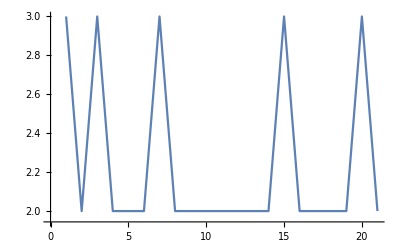

```mathematica
ListLinePlot[TsetlinCurrentState/@definite2BanditList] (* show the state of the tsetlin machine over time *)
```